# Model serology with different FOI functions

## Preliminary results from NSF eMB grant Jan 20, 2025

## Define a partial differential equation for the general case

s[a,t] gives the probability an individual of age a has negative serology at time t and λ is the force of infection (FOI).

Arbitrary force of infection:

```mathematica
PDE = D[s[a,t],t]==-λ[t]*s[a,t] - D[s[a,t],a]
```

s^(0,1)[a,t]==-s[a,t] λ[t]-s^(1,0)[a,t]

Solve the PDE assuming all individuals are born (a=0) with the probability of being susceptible =1 (i.e. s[0,t]==1).

```mathematica
DSolve[{PDE,s[0,t]==1},s[a,t],{a,t}]//FullSimplify
```

{{s[a,t]→ⅇ^(--λ[-a+t+K[1]]K[1]10+-λ[-a+t+K[1]]K[1]1a)}}

## Define a partial differential equation for the when FOI is constant

Constant force of infection with a discrete change:

```mathematica
PDE2 = D[s[a,t],t]==-λ*s[a,t] - D[s[a,t],a]
```

s^(0,1)[a,t]==-λ s[a,t]-s^(1,0)[a,t]

Solve the PDE assuming all individuals are born (a=0) with the probability of being susceptible =1 (i.e. s[0,t]==1).

```mathematica
DSolve[{PDE2, s[0,t]==1},s[a,t],{a,t}]
```

{{s[a,t]→ⅇ^(-a λ)}}

This solution is the starting condition (i.e. S[a,0]==Exp[-λ0 a]) for t=0 for all future models. This is because we assume that FOI in the past was constant and the current conditions are now changing the FOI. For all models below t>0.

## Define a partial differential equation for the when FOI is linear

Constant force of infection:

```mathematica
PDE3 = D[s[a,t],t]==-(λ0 + λ*t)*s[a,t] - D[s[a,t],a]
```

s^(0,1)[a,t]==(-t λ-λ0) s[a,t]-s^(1,0)[a,t]

Solve the PDE assuming all individuals are born (a=0) with the probability of being susceptible =1 (i.e. s[0,t]==1).

```mathematica
DSolve[{PDE3, s[0,t]==1},s[a,t],{a,t}]
```

{{s[a,t]→ⅇ^(1/2 a (a λ-2 (t λ+λ0)))}}

NOTE: PDE3 is not solvable when we add the condition S[a,0]==Exp[-λ0 a]).

## Changing FOI from constant FOI at t=0

## FOI has a starting value for λ0 and changes to a new constant value λ

When t=0 the FOI is equal to λ0:

```mathematica
PDEnew = D[s[a,t],t]==-λ*ρ*s[a,t] - D[s[a,t],a]
```

s^(0,1)[a,t]==-λ ρ s[a,t]-s^(1,0)[a,t]

```mathematica
mysol=DSolve[{PDEnew, s[0,t]==1,s[a,0]==Exp[-λ a]},s[a,t],{a,t}]//FullSimplify
```

{{s[a,t]→ⅇ^(-a λ (1+ρ)) (-ⅇ^(λ (t+a ρ-t ρ)) (-1+HeavisideTheta[-a+t])+ⅇ^(a λ) HeavisideTheta[-a+t])}}

```mathematica
pars1={λ->.008,ρ->12};
```

```mathematica
t0=s[a,t]/.mysol/.pars1/.t->0;
```

```mathematica
t5=s[a,t]/.mysol/.pars1/.t->5;
```

```mathematica
t10=s[a,t]/.mysol/.pars1/.t->10;
```

```mathematica
t15=s[a,t]/.mysol/.pars1/.t->15;
```

```mathematica
MyLegend=LineLegend[{CMYKColor[0.89,0.5,0.5,0.25],CMYKColor[0.11,0.14,0.92,0.16],CMYKColor[0.08,0.8,0.74,0.39],Gray},{"0","5","10","15","20"}, LegendLabel->"Time (t in years)",LegendMarkerSize->10,LabelStyle->8]
```

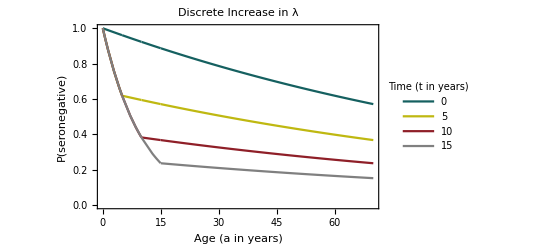

```mathematica
Pincrease=Plot[{t0,t5,t10,t15},{a,0,70},PlotStyle->{CMYKColor[0.89,0.5,0.5,0.25],CMYKColor[0.11,0.14,0.92,0.16],CMYKColor[0.08,0.8,0.74,0.39],Gray},Frame->True,FrameStyle->{{Thin,Black},{Thin,Black},{Thin,Black},{Thin,Black}},BaseStyle->{FontSize->14,FontColor->Black},FrameLabel->{"Age (a in years)","P(seronegative)"},LabelStyle->{FontColor->Black},PlotRange->{0,1},Epilog->{Inset[MyLegend,{63,0.77}]},PlotLabel->"Discrete Increase in λ"]
```

```mathematica
pars2={λ->0.05, ρ->0.1};
```

```mathematica
d0=s[a,t]/.mysol/.pars2/.t->0;
```

```mathematica
d5=s[a,t]/.mysol/.pars2/.t->5;
```

```mathematica
d10=s[a,t]/.mysol/.pars2/.t->10;
```

```mathematica
d15=s[a,t]/.mysol/.pars2/.t->15;
```

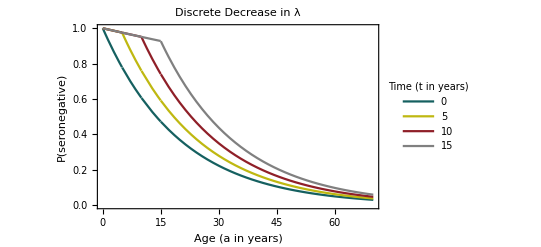

```mathematica
Pdecrease=Plot[{d0,d5,d10,d15},{a,0,70},PlotStyle->{CMYKColor[0.89,0.5,0.5,0.25],CMYKColor[0.11,0.14,0.92,0.16],CMYKColor[0.08,0.8,0.74,0.39],Gray},Frame->True,FrameStyle->{{Thin,Black},{Thin,Black},{Thin,Black},{Thin,Black}},BaseStyle->{FontSize->14,FontColor->Black},FrameLabel->{"Age (a in years)","P(seronegative)"},LabelStyle->{FontColor->Black},PlotRange->{0,1},Epilog->{Inset[MyLegend,{63,0.77}]},PlotLabel->"Discrete Decrease in λ"]
```

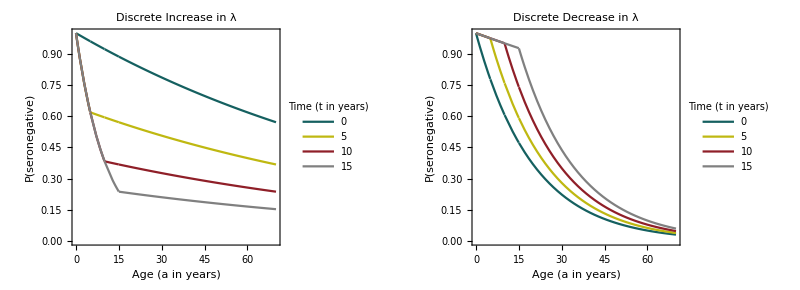

```mathematica
Figure3=GraphicsRow[{Pincrease,Pdecrease},ImageSize->800,Spacings->0]
```

```mathematica
(*Export["C:\Users\erin.clancey\Documents\FOI_eMB Grant\Figure3.png",Figure3]*)
```

## Practice ODE with waning immunity

Constant force of infection with a discrete change:

```mathematica
Sdot= D[s[a],a]==-λ*s[a]+ωR[a]
```

s'[a]==-λ s[a]+ωR[a]

```mathematica
Rdot= D[R[a],a]==λ*s[a]-ωR[a]
```

R'[a]==λ s[a]-ωR[a]

```mathematica
DSolve[{Sdot,Rdot, s[0]==1,R[0]==0},{s[a],R[a]},a]
```

{{R[a]→-ⅇ^(-a λ) (1-ⅇ^(a λ)+ⅇ^(a λ) (-ωR[K[1]]+ⅇ^(λ K[1]) (-1+ⅇ^(-λ K[1])) ωR[K[1]])K[1]10-ⅇ^(a λ) (-ωR[K[1]]+ⅇ^(λ K[1]) (-1+ⅇ^(-λ K[1])) ωR[K[1]])K[1]1a-ⅇ^(λ K[2]) ωR[K[2]]K[2]10+ⅇ^(a λ) ⅇ^(λ K[2]) ωR[K[2]]K[2]10+ⅇ^(λ K[2]) ωR[K[2]]K[2]1a-ⅇ^(a λ) ⅇ^(λ K[2]) ωR[K[2]]K[2]1a),s[a]→-ⅇ^(-a λ) (-1+ⅇ^(λ K[2]) ωR[K[2]]K[2]10-ⅇ^(λ K[2]) ωR[K[2]]K[2]1a)}}

This solution is the starting condition (i.e. S[a,0]==Exp[-λ0 a]) for t=0 for all future models. This is because we assume that FOI in the past was constant and the current conditions are now changing the FOI. For all models below t>0.

## Define a partial differential equation for the when FOI is constant: Add waning immunity

Constant force of infection with a discrete change:

```mathematica
Sdot= D[s[a,t],t]==-λ*s[a,t]+ωR - D[s[a,t],a]+D[R[a,t],a]
```

s^(0,1)[a,t]==ωR-λ s[a,t]+R^(1,0)[a,t]-s^(1,0)[a,t]

```mathematica
Rdot= D[R[a,t],t]==λ*s[a,t]-ωR + D[s[a,t],a]-D[R[a,t],a]
```

R^(0,1)[a,t]==-ωR+λ s[a,t]-R^(1,0)[a,t]+s^(1,0)[a,t]

Solve the PDE assuming all individuals are born (a=0) with the probability of being susceptible =1 (i.e. s[0,t]==1).

```mathematica
DSolve[{PDE2, s[0,t]==1},s[a,t],{a,t}]
```

{{s[a,t]→ⅇ^(-a λ)}}

This solution is the starting condition (i.e. S[a,0]==Exp[-λ0 a]) for t=0 for all future models. This is because we assume that FOI in the past was constant and the current conditions are now changing the FOI. For all models below t>0.